```mathematica
f[x_]:=Sin[Tan[x]]-Tan[Sin[x]]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

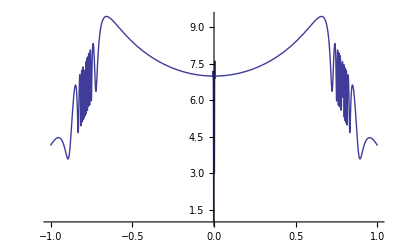

```mathematica
Plot[Log[2,f[2*x]/f[x]],{x,-1,1}]
```

```mathematica
Series[f[x],{x,0,10}]
```

-x^7/30-(29 x^9)/756+O[x]^11

```mathematica
g[x_]:=(Sinh[x]-x-x^3/6)/x^5
```

```mathematica
Limit[g[x],x->0]
```

1/120

```mathematica
h[x_]:=(1/x^2)-(1/Tan[x]^2)
```

```mathematica
Limit[h[x],x->0]
```

2/3

```mathematica
i[x_]:=(Exp[x]-x^E)/(x-E)^2
```

```mathematica
Limit[i[x],x->E]
```

ⅇ^(-1+ⅇ)/2

```mathematica
Series[Log[a^x+b^x],{x,0,2}]
```

Log[2]+1/2 (Log[a]+Log[b]) x+1/8 (Log[a]^2-2 Log[a] Log[b]+Log[b]^2) x^2+O[x]^3

```mathematica
FullSimplify[%]
```

Log[2]+1/2 (Log[a]+Log[b]) x+1/8 (Log[a]-Log[b])^2 x^2+O[x]^3

```mathematica
Series[Sqrt[Sin[x]],{x,Pi/4,2}]
```

1/2^(1/4)+(x-π/4)/(2 2^(1/4))-(3 (x-π/4)^2)/(8 2^(1/4))+O[x-π/4]^3

```mathematica
Series[Exp[Sqrt[1+x]],{x,0,3}]
```

ⅇ+(ⅇ x)/2+(ⅇ x^3)/48+O[x]^4

```mathematica
3/48-1/16+1/(6*8)
```

1/48

```mathematica
Series[Sqrt[1+Cos[x]],{x,0,4}]
```

√2-x^2/(4 √2)+x^4/(192 √2)+O[x]^5

```mathematica
%*Sqrt[2]
```

2-x^2/4+x^4/192+O[x]^5

```mathematica
4*48
```

192

```mathematica
1/96-1/128
```

1/384

```mathematica
%*2
```

1/192

```mathematica
Series[Cos[x],{x,0,4}]
```

1-x^2/2+x^4/24+O[x]^5

```mathematica
F[x_]:=1/x-1/(2*Sin[x/2])
```

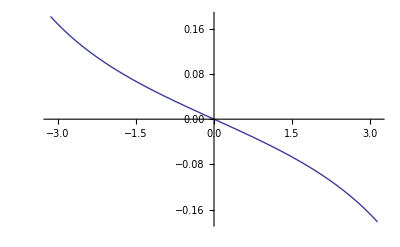

```mathematica
Plot[F[x],{x,-Pi,Pi}]
```

```mathematica
D[F[x],x]
```

-1/x^2+1/4 Cot[x/2] Csc[x/2]

```mathematica
Plot[D[F[x],x],{x,-Pi,Pi}]
```

General::ivar: -3.14146 is not a valid variable.

General::ivar: -3.01324 is not a valid variable.

General::ivar: -2.88501 is not a valid variable.

General::stop: Further output of General :: ivar will be suppressed during this calculation.

-Graphics-

```mathematica
Limit[Log[x+1]/Log[x],x->Infinity]
```

1

```mathematica
Series[Log[1+x],{x,0,2}]
```

x-x^2/2+O[x]^3

```mathematica
Limit[(x/Log[1+x]-1)/x,x->0]
```

1/2

```mathematica
Solve[Log[1+x]==x/(1+y*x),y]
```

{{y→(x-Log[1+x])/(x Log[1+x])}}

```mathematica
x/(1+x*y)/.Solve[Log[1+x]==x/(1+y*x),y]
```

{x/(1+(x-Log[1+x])/Log[1+x])}

```mathematica
FullSimplify[%]
```

{Log[1+x]}

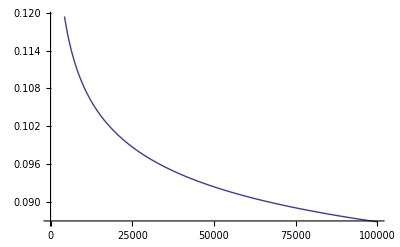

```mathematica
Plot[(x/Log[1+x]-1)/x,{x,0,100000}]
```

```mathematica
Series[α^x,{x,0,2}]
```

1+Log[α] x+1/2 Log[α]^2 x^2+O[x]^3

```mathematica
Series[β^x,{x,0,2}]
```

1+Log[β] x+1/2 Log[β]^2 x^2+O[x]^3

```mathematica
Series[α^x,{x,0,2}]+Series[β^x,{x,0,2}]
```

2+(Log[α]+Log[β]) x+(Log[α]^2/2+Log[β]^2/2) x^2+O[x]^3

```mathematica
FullSimplify[Series[Log[%],{x,0,2}]]
```

Log[2]+1/2 (Log[α]+Log[β]) x+1/8 (Log[α]-Log[β])^2 x^2+O[x]^3

```mathematica
X=(x/2)*(Log[α]+Log[β])+(x^2/4)*(Log[α]^2+Log[β]^2)+O[x]^3
```

1/2 (Log[α]+Log[β]) x+1/4 (Log[α]^2+Log[β]^2) x^2+O[x]^3

```mathematica
X^2
```

1/4 (Log[α]+Log[β])^2 x^2+1/4 (Log[α]+Log[β]) (Log[α]^2+Log[β]^2) x^3+O[x]^4

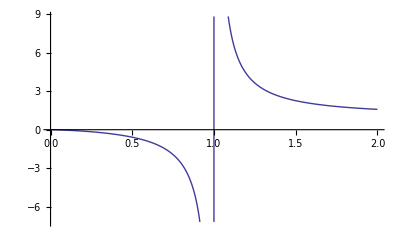

```mathematica
Plot[Log[x+1]/Log[x],{x,0,2}]
```

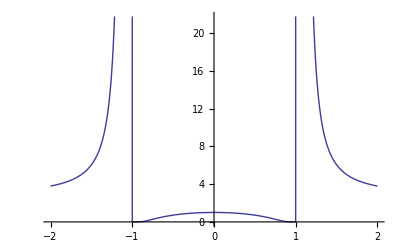

```mathematica
Plot[Exp[x^2/(x^2-1)],{x,-2,2}]
```

```mathematica
Limit[Exp[x^2/(x^2-1)],x->Infinity]
```

ⅇ

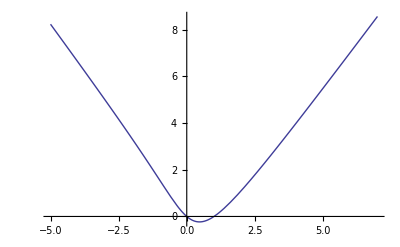

```mathematica
Plot[(x-1)*ArcTan[x],{x,-5,7}]
```

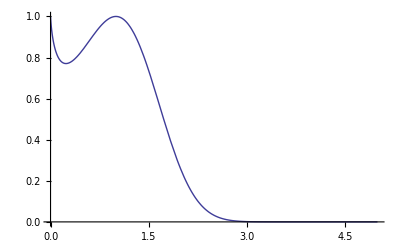

```mathematica
Plot[x^(x-x^2),{x,0,5}]
```

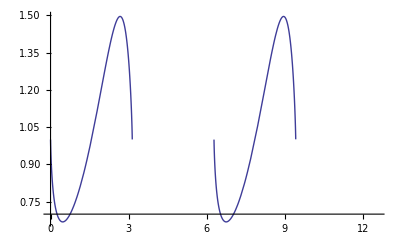

```mathematica
Plot[Sin[x]^Tan[x],{x,0,4*Pi}]
```